### From other notebooks

```mathematica
precompute[positions_,perturbedIndex_,s_,ν_, θ_]:= Block[
{
dp = Differences[positions],
betaList,
diffs,
reducedAngles
},
betaList =ArcTan@@@ Join[-dp[[1;;perturbedIndex-1]],dp[[perturbedIndex;;-1]]] ;
reducedAngles=θ +2 ArcCot[ⅇ^(-s+s ν)Cot[(betaList-θ)/2]];
reducedAngles=Insert[reducedAngles,θ,perturbedIndex];
Transpose@{Cos[reducedAngles],Sin[reducedAngles]}]
```

```mathematica
displacements[perturbedIndex_,positionList_,s_,ν_,θ_]:= 
Block[{newPositions,betaList,Δ  },
Δ=precompute[positionList,perturbedIndex,s,ν,θ];
newPositions[perturbedIndex] =positionList[[perturbedIndex]]+s AngleVector[θ];
newPositions[index_] := newPositions[index]=
Module[{nextIndex=index-Sign[index-perturbedIndex]},
newPositions[nextIndex] + Δ[[index]]
];
newPositions/@Range[Length[Δ]]
]
```

```mathematica
chainGraphic[positions_]:= 
{FaceForm[Orange],EdgeForm[Black],Disk[#,1/2]&/@(positions),
MapIndexed[Text[#2[[1]],#1]&,(positions)]}
```

## Work on newton’s method for removing overlap

#### An example that works almost immediately. Here the overlap is fairly simple. A more complicated case can be queried by using this initial state: positions=displacements[11,positions,.5,.1,0]; Really complicated from this positions=displacements[11,positions,1,.1,0]; But, I am not sure if there is a guaranteed that it will always work. Question is: Do the complicated cases really matter? It is unlikely that the algorithm is so bad that we would ever reach one. But, it is unsatisfying that the algorithm may never return in a bizarre side case.

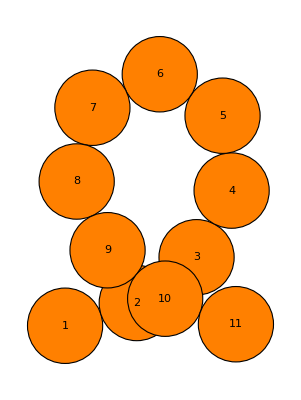

```mathematica
positions=AnglePath[ConstantArray[0.565,10]];
positions=displacements[11,positions,.7,.1,0];
nf= Nearest[positions->All];
Graphics[chainGraphic[positions]]
```

#### Neighbor finding with distance, collision checking

```mathematica
findNotNearestNeighborUpToDistance[positions_,nf_,whichParticle_,beyondNearstNeighbor_, distance_]:=Block[{nnn},
nnn=Select[Abs[#Index-whichParticle] >1 &][nf[positions[[whichParticle]],{beyondNearstNeighbor + 3,distance}]];
Which[
nnn!={},Join[<|"Me"-> whichParticle|>,#]&/@nnn,
True,{}
]
]
```

```mathematica
findAllNotNearestNeighborUpToDistance[positions_,nf_,beyondNearstNeighbor_, distance_]:=findNotNearestNeighborUpToDistance[positions,nf,#,beyondNearstNeighbor, distance]&/@Range[Length[positions]]
```

```mathematica
findAllNotNearestNeighborUpToDistance[positions,nf,13,1]
```

{{<|Me→1,Element→{-0.916202,0.038069},Index→11,Distance→0.123573|>},{},{},{},{},{},{},{},{},{},{<|Me→11,Element→{-0.796804,0.00621832},Index→1,Distance→0.123573|>}}

```mathematica
countCollisions[positions_,nf_]:= Block[{numberOverlaps=0},
Do[
numberOverlaps = Length[
Select[
Abs[#Index-particleIndex]>1 &&#Distance < 1&][ nf[positions[[particleIndex]],13]]
];
If[numberOverlaps>0,Return[numberOverlaps]],
{particleIndex,1,Length[positions]}];
numberOverlaps

]
```

### Overlap force

```mathematica
force[pMe:{xMe_,yMe_},pOther:{xOther_,yOther_}]:= Block[{dp = pOther-pMe,magSq},
magSq= dp.dp;
(-dp (1-magSq))/(magSq)^4]
```

### Neighborhood is a result from findAllNotNearestNeighborUpToDistance

```mathematica
computeForceInNeighborhood[positions_,neighborhood_List]:=
Block[{ positionList,position,myIndex},
If[Length[neighborhood]==0,Return[<|"Force"->{0,0}|>]];
myIndex = neighborhood[[1,"Me"]];
positionList =neighborhood[[All,"Element"]];
position=positions[[myIndex]];
<|"Index"->myIndex,"Force"->Total[force[position,#]&/@positionList]|>
]
```

```mathematica
(*displacements[perturbedIndex_,positionList_,s_,ν_,θ_]*)
```

### relaxOverlaps: find overlapping neighborhoods: assumption is that is never called unless there are overlaps. Nearest function is passed to computeForceInNeighborhood Find all non-zero forces Use either the largest total force on a single particle to move it, or randomly select a force.

```mathematica
relaxOverlaps[positions_, nf_]:= Block[
{},
overlappingNeighborhoods=findAllNotNearestNeighborUpToDistance[positions,nf,13, 1];
forces =computeForceInNeighborhood[positions,#]&/@overlappingNeighborhoods;
(*Echo[forces];*)
forces =Select[#Force!={0,0}&][forces];
(*Echo[forces];*)
largestForce =First[MaximalBy[forces,Norm[#Force]&]];
(*interesting, using the largest force tends to get stuck in a local minimum*)
randomForce = RandomChoice[forces];
(*Echo[largestForce];*)
displacements[largestForce["Index"],
positions,
Min[{Norm[largestForce["Force"]],0.01}] (*hack to limit how far a particle is pushed*),
0,
ArcTan@@largestForce["Force"]]
(*displacements[perturbedIndex_,positionList_,s_,ν_,θ_]*)
]
```

#### Testing

```mathematica
relaxedPositions= positions;
originalGraphic = Graphics[chainGraphic[relaxedPositions]];
nf =Nearest[relaxedPositions->All];
graphic= Graphics[chainGraphic[relaxedPositions]]
```

-Graphics-

```mathematica
relaxOverlaps[relaxedPositions,nf]
```

{{-2.66697,0.23747},{-1.69975,0.491381},{-0.881476,1.06621},{-0.399587,1.94245},{-0.537854,2.93284},{-1.40205,3.436},{-2.27486,2.94795},{-2.47752,1.9687},{-2.09192,1.04603},{-1.3555,0.369508},{-0.434008,-0.018889}}

```mathematica
Do[
If[Flatten[findAllNotNearestNeighborUpToDistance[relaxedPositions,nf,13,1]]=={} (*not the most efficient collision detector, use throw instead*),Break[]];
relaxedPositions =relaxOverlaps[relaxedPositions,nf];
nf =Nearest[relaxedPositions->All];
graphic = chainGraphic[relaxedPositions];
Pause[0.05]
,
{1000}
]
```

$Aborted

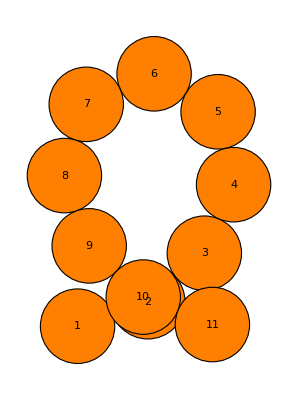

```mathematica
Row[{originalGraphic,Dynamic[Graphics[graphic]]}]
```